```mathematica
l[p_]:=Likelihood[BinomialDistribution[100,p],{10}]
```

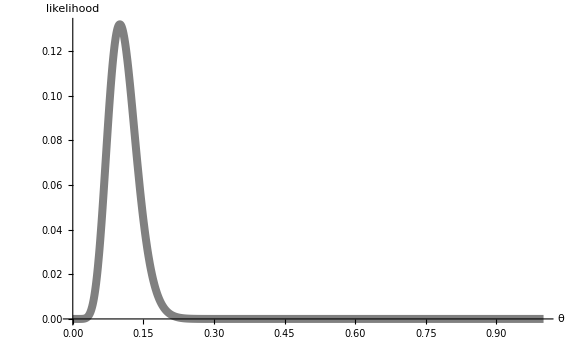

```mathematica
Show[Plot[l[p],{p,0,1},PlotRange->{Automatic,Full},PlotStyle->{Gray,Thickness[0.01]},AxesLabel->{θ,likelihood},BaseStyle->{FontSize->16}],ImageSize->Large]
```

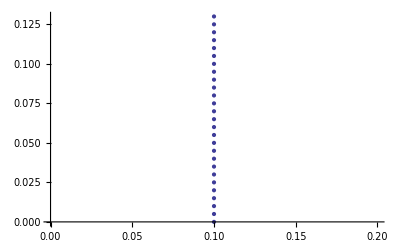

```mathematica
x=Table[0.1,{27}];
y= Table[i,{i,0,0.13,0.005}];
ListPlot[Thread[{x,y}]]
```

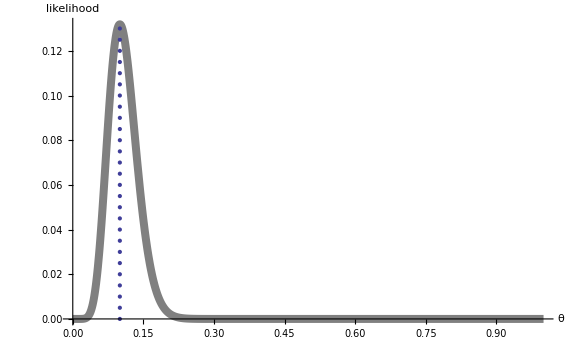

```mathematica
Show[Plot[l[p],{p,0,1},PlotRange->{Automatic,Full},PlotStyle->{Gray,Thickness[0.01]},AxesLabel->{θ,likelihood},BaseStyle->{FontSize->16}],ListPlot[Thread[{x,y}]],ImageSize->Large]
```